```mathematica
G=6.67*^-11m^3 kg^-1 s^-2;
mp=1.672*^-27kg;
k=1.380*^-23kg m^2 s^-2  Kk^-1;
Msun=1.989*^30kg;
Rsun=6.9599*^8m;
σ=5.67*^-1erg m^-2 s^-1 Kk^-4;
h=6.626*^-34kg m^2 s^-1;
Tth[M_,R_]:=G M mp /(3 k R);
Tb[M_,R_]:=(1.3*^38M erg/s /(4π R^2 σ Msun))^(1/4);
```

```mathematica
Tth[1Msun,1*^4m]
Tb[1Msun,1*^4m]
```

5.35792×10^11 Kk

2.06675×10^7 (Kk^4)^(1/4)

```mathematica
c=3*^8m/s;
Rs[M_]:=6G M/c^2
```

```mathematica
Tth[10^8Msun,3*^16m]
Tb[10^8Msun,3*^16m]
```

1.78597×10^7 Kk

1193.24 (Kk^4)^(1/4)

```mathematica
Dr[r_,M_,Md_]:=(5*^30)((M/Msun)^-2 Md/(1*^30kg/s))r^-3 f[r,M];
f[r_,M_]:=1-(6 /r)^(1/2);
T[r_,M_]:=(5*^7Kk)(α M/Msun)^(-1/4)r^(-3/8);
Int[R_,v_,M_,Md_]:=R/((Exp[h v /k /T[R m/Rs[M],M]]-1)(Dr[R m/Rs[M],M,Md])^2);
F[v_,M_,Md_,i_]:=(4π h v^3 Cos[i])/c^2 m^2 NIntegrate[Int[R,v,M,Md],{R,Rs[M]/m,250/6 Rs[M]/m}];
Rin=1Rsun/m;
Rout=200Rsun/m;
α=1;
```

```mathematica
drawlist[M_,Md_]:=Table[{i,F[10^i s^-1,M*Msun,Md/365/3600/24Msun/s,π/4]*1*^7/(kg m^2) s^2},{i,1,20,0.1}];
```

```mathematica
TTT=Flatten[Table[drawlist[i,j],{i,{10^6,10^8,10^10}},{j,{0.1,1,10}}],1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in R near {R} = {5.30955×10^10}. NIntegrate obtained 8.98687×10^26 and 7.06282×10^26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in R near {R} = {5.30955×10^10}. NIntegrate obtained 8.44509×10^26 and 7.06313×10^26 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in R near {R} = {5.30955×10^10}. NIntegrate obtained 6.4186×10^26 and 5.29817×10^26 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

```mathematica
Needs["PlotLegends`"]
```

```mathematica
ListLogPlot[TTT,Joined->True,AxesLabel->{"Log[v(Hz)]","Flux(erg/s/Hz)"},PlotStyle->Flatten[Table[{i,j},{i,{Dotted,Dashed,Thick}},{j,{Red,Green,Blue}}],1],PlotLegend->Flatten[Table["10E"~~i~~"M_s, "~~j~~"M_s/yr",{i,{"6","8","10"}},{j,{"0.1","1","10"}}],1],LegendPosition->{1,-0.5},LegendSize->{0.6,1},LegendShadow->None,ImageSize->500]
```

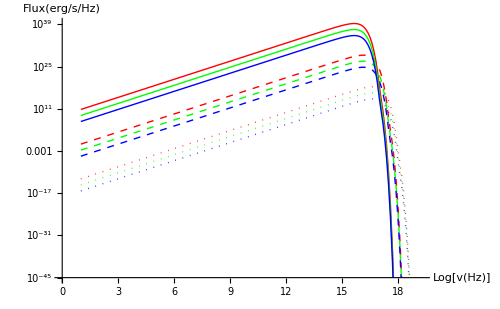

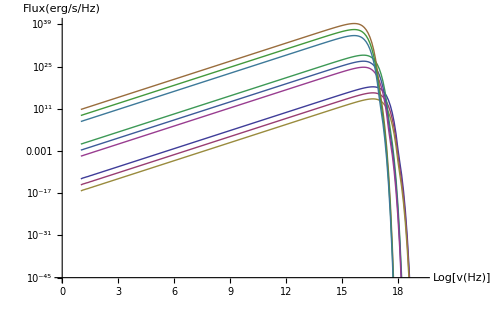

```mathematica
Flatten[Table[{i.j},{i,{Dotted,Dashed,Thick}},{j,{Red,Green,Blue}}],1]
```

{{Dashing[{0,Small}].RGBColor[1,0,0]},{Dashing[{0,Small}].RGBColor[0,1,0]},{Dashing[{0,Small}].RGBColor[0,0,1]},{Dashing[{Small,Small}].RGBColor[1,0,0]},{Dashing[{Small,Small}].RGBColor[0,1,0]},{Dashing[{Small,Small}].RGBColor[0,0,1]},{Thickness[Large].RGBColor[1,0,0]},{Thickness[Large].RGBColor[0,1,0]},{Thickness[Large].RGBColor[0,0,1]}}